```mathematica
t
```

#### 1

```mathematica
MatrizSimilitudTopologica[listaGrafos_List]:=Module[{vectoresEspectrales,matrizDistancias},(*1. Calcular los autovalores numéricos y ordenados para cada grafo*)vectoresEspectrales=Table[Sort[Eigenvalues[N[Normal[KirchhoffMatrix[g]]]]],{g,listaGrafos}];
(*2. Calcular la matriz de distancias euclidianas entre todos los espectros*)matrizDistancias=DistanceMatrix[vectoresEspectrales,DistanceFunction->BinaryDistance];
(*3. Convertir las distancias en similitudes usando la fórmula 1/(1+d)*)1/(1+matrizDistancias)]
```

```mathematica
r23;
```

```mathematica
evos=ParallelTable[
inits=IntegerDigits[#,2,space]&/@Range[0,2^space-1];
graphs=Table[
conect=Map[
CaArray[r23[[i]],#,1][[1]]->CaArray[r23[[i]],#,1][[2]]&,
inits];
r23[[i]]->Graph[conect],
{i,1,Length[r23]}];
graphs,
{space,1,10}];
```

```mathematica
distances=ParallelTable[MatrizSimilitudTopologica[evos[[i,;;,2]]],{i,1,10}];
```

DistanceMatrix::mlmpty: The dataset should contain at least one informative example (non-missing) for training.

General::stop: Further output of DistanceMatrix::mlmpty will be suppressed during this calculation.

DistanceMatrix::mlmpty: The dataset should contain at least one informative example (non-missing) for training.

General::stop: Further output of DistanceMatrix::mlmpty will be suppressed during this calculation.

```mathematica
m=Mean[distances];
```

```mathematica
DeleteDuplicates[Flatten[m]];
```

Estas son las reglas que son iguales segun el analisis de similitud topologica de todas las condiciones iniciales posibles para multiples tamaños. Podemos seguir expandiendo el tamaño de la condición inicial yestas reglas siguen siendo equivalentes. Hay 173 reglas de las 256 que estan en estas agrupaciones. Entonces de esta forma reducimos a 83 pendientes de clasificar.

```mathematica
equals=DeleteDuplicates[Sort/@Select[Position[m,x_/;x>=1]-1,#[[1]]=!=#[[2]]&]];
DeleteDuplicates[Flatten[equals]]//Length
```

0

```mathematica
equals
```

{}

```mathematica
knowr=Subscript[#,2,3]&/@Sort[DeleteDuplicates[Flatten[equals]]];
```

```mathematica
Complement[Sort[Select[DeleteDuplicates[VertexList[Flatten[Values[addData[knowr]]]]],#[[2]]==2&&#[[3]]==3&][[;;,1]]],knowr[[;;,1]]]
```

Values::invrl: The argument addData[{}] is not a valid Association or a list of rules.

VertexList::graph: A graph object is expected at position 1 in VertexList[Values[addData[{}]]].

Part::partw: Part 2 of Values[addData[{}]] does not exist.

Part::partw: Part 3 of Values[addData[{}]] does not exist.

VertexList::argt: VertexList called with 0 arguments; 1 or 2 arguments are expected.

Complement::heads: Heads List and VertexList at positions 2 and 1 are expected to be the same.

Complement[VertexList[],{}]

```mathematica
addData[Subscript[#,2,3]&/@{9,49,65,84,107,118,120,145,213}]
```

addData[{9_(2,3),49_(2,3),65_(2,3),84_(2,3),107_(2,3),118_(2,3),120_(2,3),145_(2,3),213_(2,3)}]

```mathematica
distances[[;;,10,112]]
m[[10,112]]
```

Part::partw: Part 10 of 1/(1+DistanceMatrix[{},DistanceFunction→BinaryDistance]) does not exist.

{1/(1+DistanceMatrix[{},DistanceFunction→BinaryDistance]),1/(1+DistanceMatrix[{},DistanceFunction→BinaryDistance]),1/(1+DistanceMatrix[{},DistanceFunction→BinaryDistance]),1/(1+DistanceMatrix[{},DistanceFunction→BinaryDistance]),1/(1+DistanceMatrix[{},DistanceFunction→BinaryDistance]),1/(1+DistanceMatrix[{},DistanceFunction→BinaryDistance]),1/(1+DistanceMatrix[{},DistanceFunction→BinaryDistance]),1/(1+DistanceMatrix[{},DistanceFunction→BinaryDistance]),1/(1+DistanceMatrix[{},DistanceFunction→BinaryDistance]),1/(1+DistanceMatrix[{},DistanceFunction→BinaryDistance])}⟦1;;All,10,112⟧

Part::partw: Part 10 of 1/(1+DistanceMatrix[{},DistanceFunction→BinaryDistance]) does not exist.

1/(1+DistanceMatrix[{},DistanceFunction→BinaryDistance])⟦10,112⟧

```mathematica
FirmaEspectral[g_Graph]:=Module[{x},CoefficientList[CharacteristicPolynomial[Normal@AdjacencyMatrix[g],x],x]]
```

```mathematica
FirmaEspectral[evos[[10,1,2]]]
```

Part::partw: Part 1 of {} does not exist.

FirmaEspectral[{{},{},{},{},{},{},{},{},{},{}}⟦10,1,2⟧]

#### Propuesta de claude

la propuesta que estaba manejando con los gafos no estaba mal pero claude corrigio una cosas que no habia considerado pero es para eliminar la similitud entre los grafos.

```mathematica
r23=Subscript[#,2,3]&/@Range[0,255];
```

Utilizamos la firma espectral que utiliza los EigenValues de las posibles conexiones de un grafo. Entre mas nodos le pasemos mejor sera la información que obtengamos, La firma espectral es como si vieramos el grafo como una telaraña, si tiramos de un nodo como afecta a las vibraciones de las otros nodos. Por ejemplo, estas son las firmas espectrales de la regla 3 con condiciones iniciales de tamaño diferente.

```mathematica
FirmaEspectral[g_Graph]:=CoefficientList[CharacteristicPolynomial[Normal@AdjacencyMatrix[g],x],x]
```

```mathematica
#[[1]]->FirmaEspectral[#[[2]]]&/@evos[r23[[31;;31]],#]&/@Range[2,6,2]
```

{{30_(2,3)→{0,-1,3,-3,1}},{30_(2,3)→{0,0,0,0,0,1,-3,3,-1,0,0,0,0,-1,3,-3,1}},{30_(2,3)→{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,3,-3,1}}}

Si seguimos la teoria que llevamos diciendo que las versiones en espejo y la permuatación de estados son equivalentes, entonces sus firmas espectrales deben de ser equivalentes. Para la regla 30, estas 4 reglas son equivalentes: {30_(2,3),86_(2,3),135_(2,3),149_(2,3)}. Vemos que la firma espectral de todas estas reglas es la misma

```mathematica
r30Evos=evos[{Subscript[30, 2,3],Subscript[86, 2,3],Subscript[135, 2,3],Subscript[149, 2,3]},#]&/@Range[2,6,2];
Grid[
Prepend[
Table[FirmaEspectral[#[[2]]]&/@r30Evos[[i]],
{i,1,Length[r30Evos]}]
,{Subscript[30, 2,3],Subscript[86, 2,3],Subscript[135, 2,3],Subscript[149, 2,3]}
],Frame->All]
```

30_(2,3) | 86_(2,3) | 135_(2,3) | 149_(2,3)
{0,-1,3,-3,1} | {0,-1,3,-3,1} | {0,-1,3,-3,1} | {0,-1,3,-3,1}
{0,0,0,0,0,1,-3,3,-1,0,0,0,0,-1,3,-3,1} | {0,0,0,0,0,1,-3,3,-1,0,0,0,0,-1,3,-3,1} | {0,0,0,0,0,1,-3,3,-1,0,0,0,0,-1,3,-3,1} | {0,0,0,0,0,1,-3,3,-1,0,0,0,0,-1,3,-3,1}
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,3,-3,1} | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,3,-3,1} | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,3,-3,1} | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,3,-3,1}

Sin embargo, para tener una aproximación 100% perfecta usamos los los grafos isomorficos. Vemos que ahora podemos agrupar todas las reglas, y vemos que el grafo isomorfico de todas estasn 4 reglas estan agrupados.

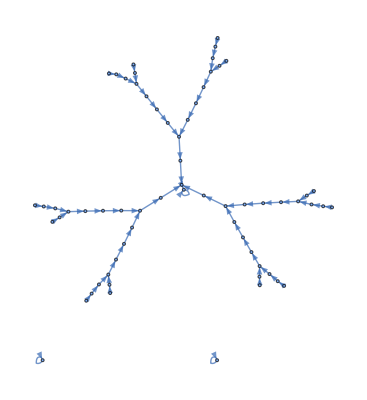
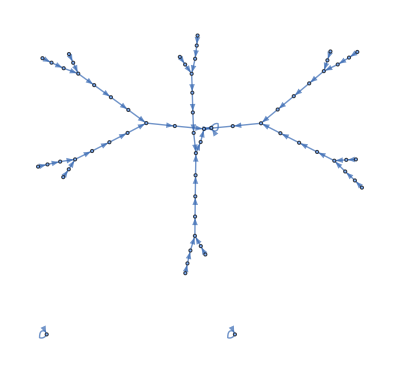
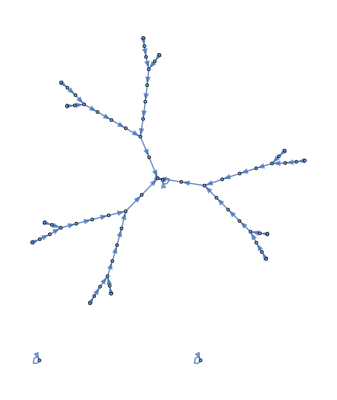
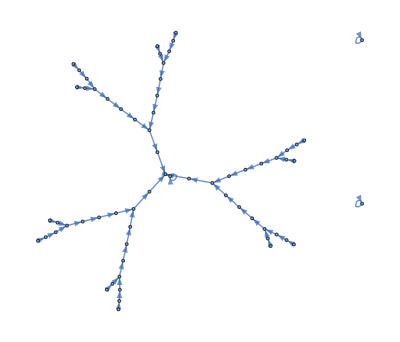
{{30_(2,3)→-Graphics-,86_(2,3)→-Graphics-,135_(2,3)→-Graphics-,149_(2,3)→-Graphics-}}

```mathematica
Gather[r30Evos[[-1]],IsomorphicGraphQ[#1[[2]],#2[[2]]]&]
```

La firma de los grafos isomorficos en teoria deberia de ser igual, pero existen casos de grafos espectrales no isomorficos, es decir, su firma es identica pero no su versión isomorfica. Entonces el primer filtro tiene que ser encontrar las relaciones isomorficas, esto nos permite verificar si son iguales, despues, podemos usar la firma espectral para medir la diferencia.
La firma puede tener falsos positivos.

Ahora vamos a probar encontrar las mismas relaciones que ya habiamos encontrado, encontrar las versiones isomorficas de todas las reglas deberia de guiarnos a encontrar nuevas relaciones. Estas son las clases de equivalencia que podemos encontrar con 1 solo espacio.

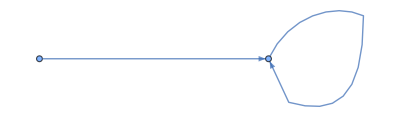
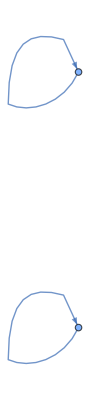
-Graphics- | -Graphics- | -Graphics-
Total:128 | Total:64 | Total:64
{0_(2,3),2_(2,3),4_(2,3),6_(2,3),8_(2,3),10_(2,3),12_(2,3),14_(2,3),16_(2,3),18_(2,3)} | {1_(2,3),3_(2,3),5_(2,3),7_(2,3),9_(2,3),11_(2,3),13_(2,3),15_(2,3),17_(2,3),19_(2,3)} | {128_(2,3),130_(2,3),132_(2,3),134_(2,3),136_(2,3),138_(2,3),140_(2,3),142_(2,3),144_(2,3),146_(2,3)}

```mathematica
gr23i1=Gather[evos[r23,1],IsomorphicGraphQ[#1[[2]],#2[[2]]]&];
Grid@Transpose[{#[[1,2]],"Total:"<>ToString[Length[#]],#[[;;UpTo[10],1]]}&/@gr23i1]
```

Los siguientes resultados muestran como aumenta estas distribuciones conforme vamos aumentando el espacio.

```mathematica
r23evos=evos[r23,i]&/@Range[1,8];
```

```mathematica
gr23=ParallelTable[Gather[evos[r23,i],IsomorphicGraphQ[#1[[2]],#2[[2]]]&],{i,1,8}];
gr23=#[[1,2]]->#[[;;,1]]&/@#&/@gr23;
Iconize[gr23]
```

```mathematica
gr23=;
```

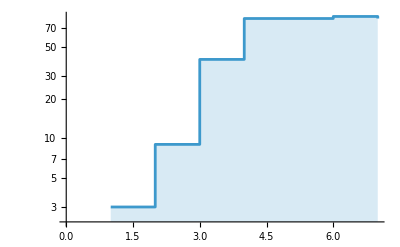

```mathematica
ListLinePlot[Length/@gr23,Filling->Bottom,ScalingFunctions->"Log",InterpolationOrder->0]
```

vemos que conforme vamos aumentando el tamaño de la vecindad, los comportamientos crecen exponencialmente hasta un limite. Para ECA este limite esta cerca del 82. Ya no puede crecer mucho mas que eso. Sin embargo, vemos que con 6 crece a 85, lo que nos indica que no es un limite absoluto, pero si de aproximación. Parece que nos acercamos a un limite.
Vamos a analizar que pasa con el 4 y ver que tanto se parecen estas relaciones.

Antes de eso, en la varaible wkr23 se guardan los grupos ya conocidos de estas reglas, para coocer las diferencias.

```mathematica
wkr23=SortBy[WeaklyConnectedComponents[Flatten[Values[addData[r23][[{"inverse","mirror"}]]]]],Min[#[[1,1]]]&];
gr23s4=gr23[[4,;;,2]];
"wkr23: "<>ToString[Length[wkr23]]<>"\ngr23s4: "<>ToString[Length[gr23s4]]
```

wkr23: 88
gr23s4: 82

vemos que existe una diferencia muy leve de agrupamiento de comportamientos, esto se debe principalmente, a que al no tener suficiente tamaño, hay comportamientos que se estan agrupando como similiares, los cuales son los siguientes:

```mathematica
fusions=Select[Table[{g,Select[wkr23,SubsetQ[g,#]&]},{g,gr23s4}],Length[#[[2]]]>1&];
Grid[fusions,Frame->All]
```

{15_(2,3),85_(2,3),170_(2,3),240_(2,3)} | {{15_(2,3),85_(2,3)},{240_(2,3),170_(2,3)}}
{23_(2,3),178_(2,3)} | {{23_(2,3)},{178_(2,3)}}
{25_(2,3),45_(2,3),61_(2,3),67_(2,3),75_(2,3),89_(2,3),101_(2,3),103_(2,3)} | {{45_(2,3),75_(2,3),101_(2,3),89_(2,3)},{67_(2,3),61_(2,3),25_(2,3),103_(2,3)}}
{28_(2,3),70_(2,3),78_(2,3),92_(2,3),141_(2,3),157_(2,3),197_(2,3),199_(2,3)} | {{28_(2,3),199_(2,3),70_(2,3),157_(2,3)},{78_(2,3),141_(2,3),92_(2,3),197_(2,3)}}
{77_(2,3),232_(2,3)} | {{77_(2,3)},{232_(2,3)}}
{105_(2,3),150_(2,3)} | {{105_(2,3)},{150_(2,3)}}

El comportamiento por grafos esta considerando que estas reglas son similares, y lo son?? Ciertamente se parecen pero no son precisamente iguales:

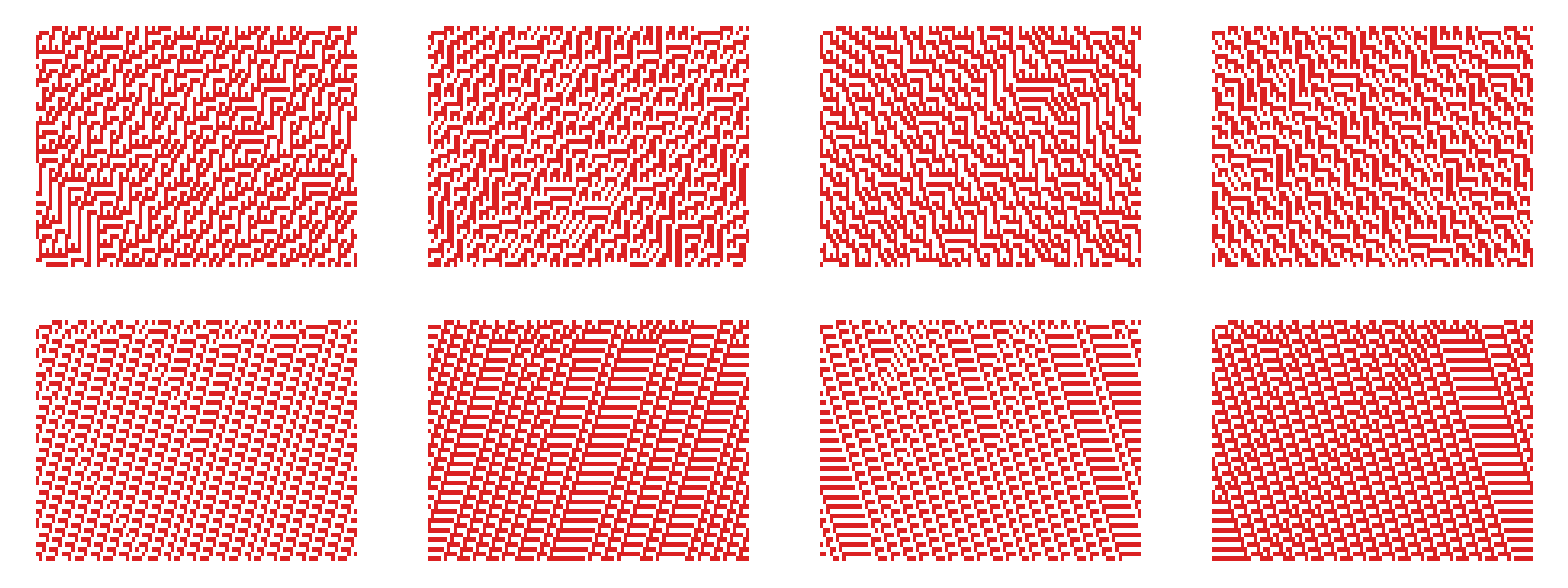

```mathematica
init=RandomInteger[{0,1},100];
Grid[CaArrayPlot[#,init,50,ImageSize->250]&/@#&/@{{Subscript[45, 2,3],Subscript[75, 2,3],Subscript[101, 2,3],Subscript[89, 2,3]},{Subscript[67, 2,3],Subscript[61, 2,3],Subscript[25, 2,3],Subscript[103, 2,3]}}]
```

Sin embargo, es una buena aproximación. Por que por otro metodo descubrimos que la diferencia es solo de 6 grupos. 
Otra cosa es que los grupos creados por lso grafos siempre son composiciones de otros conjuntos, es decir, no existen 2 reglas agrupadas por grafos y no por el metodo tradicional, puede agruparse mas de uno, pero siempre se corresponden. La funcion de abajo lo verifica y es True para todos los espacios

```mathematica
canon[part_]:=Sort[Sort/@part];
RefinaQ[fina_,gruesa_]:=AllTrue[fina,Function[c,Count[gruesa,g_/;SubsetQ[g,c]]==1]]
RefinaQ[wkr23,#[[;;,2]]]&/@gr23
```

{True,True,True,True,True,True,True}

```mathematica
fusions=Table[Select[Table[{g,Select[wkr23,SubsetQ[g,#]&]},{g,gr23[[j,;;,2]]}],Length[#[[2]]]>1&],{j,1,7}];
joints={Length[#[[1]]],Length[#[[2]]]}&/@#&/@fusions;
Grid[{Grid[#,Frame->All]&/@joints}];
```

Otra prueba que podemos realizar es con espacios mas grandes, aunque ya vimos que con 4 podemos encontrar buenas similitudes. Tenemos 2 preguntas entonces: ¿Cual es el minimo para tener un valor casi identico al real y cual es el tamaño del espacio que nos da exactamente el mismo tamaño?
Por ahora, vamos a analizar la firma espectral de los conjuntos y verificar si es siempre identica en los subjuntos, o si tenemos esos casos excepcionales:

```mathematica
space=7;
gbg=FirmaEspectral[#[[1]]]->#[[2]]&/@gr23[[space]];
gbf=GroupBy[r23,FirmaEspectral[evos[{#},space][[1,2]]]&];
Sort[Sort/@gbg[[;;,2]]]==Sort[Sort/@Values[gbf]]
```

True

jodel, ya lo habia avanzado y no lo guarde. Ni modo, lo que decia es que podemos usar la distancia de similitud para ver como se comparan las distancias por firma espectral

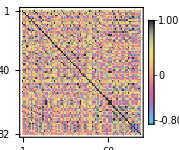
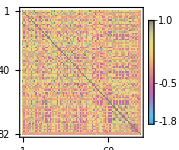
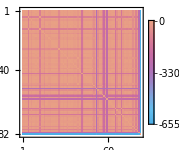
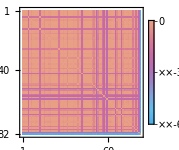
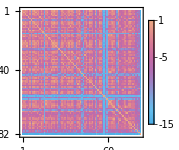
CosineDistance | BrayCurtisDistance | ManhattanDistance | SquaredEuclideanDistance | CanberraDistance
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
firmas=FirmaEspectral/@gr23[[4,;;,1]];
distances={CosineDistance,BrayCurtisDistance,ManhattanDistance,SquaredEuclideanDistance,CanberraDistance};
matrix=1-DistanceMatrix[firmas,DistanceFunction->#]&/@distances;
Grid[{distances,MatrixPlot[#,ColorFunction->"CMYKColors",ImageSize->150,PlotLegends->Automatic]&/@matrix[[;;]]}]
```

Sin embargo, si totmamos un vistazo mas de cerca, vemos que las elas ultimas evoluciones, todas tienden a clasificarlo de loa misma forma, veamos los ultimos puntos medidos, para verificar sus distancias:

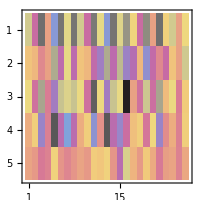
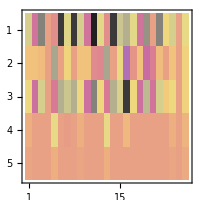
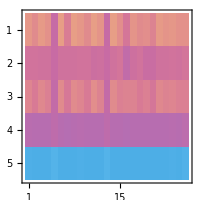
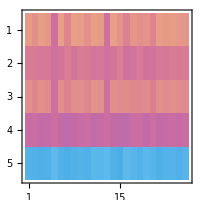
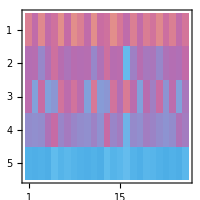
CosineDistance | BrayCurtisDistance | ManhattanDistance | SquaredEuclideanDistance | CanberraDistance
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{distances,MatrixPlot[#,ColorFunction->"CMYKColors",ImageSize->200]&/@matrix[[;;,-5;;,;;25]]}]
```

Todas tienden a asignar a la mayor distancia a excepción de la distancia coseno, no es una prueba verifica, pero es una una sustancial para emepzar a arealizar pruebas con ella.

Ahora bien, ya tenemos una propuesta de similitud... ¿Como la probamos?, que tenemos en el estado del arte que nos diga que 2 reglas se parecen?? Lo unico que se me ocurre son las reglas life like. Podemos hacerlo segun la clasificación de Wolfram, pero son solo 4 clases, igual seria interesante... o ver el resto....

Tenemos un problema, y es que para una dimension ya es dificil de calcular, para 2 es muchisimo mas.

Vamos a ver los conteos, no podemos usar 4, tiene que ser mayor.

```mathematica
ev23=evos[r23,8];
```

```mathematica
firmas=ParallelMap[FirmaEspectral,ev23[[;;,2]]];
matrix=1-DistanceMatrix[firmas,DistanceFunction->CosineDistance];
Iconize[matrix]
```

```mathematica
gr23=Gather[ev23,IsomorphicGraphQ[#1[[2]],#2[[2]]]&];
gr23=#[[1,2]]->#[[;;,1]]&/@gr23;
Iconize[gr23]
```

```mathematica
evos[rules_,space_]:=Module[{conect,inits},
ParallelTable[
inits=IntegerDigits[#,2,space]&/@Range[0,2^space-1];
conect=Map[
CaArray[rules[[i]],#,1][[1]]->CaArray[rules[[i]],#,1][[2]]&,
inits];
rules[[i]]->Graph[conect],
{i,1,Length[rules]}]
]
```

```mathematica
CaArray[ca_Subscript,s_,t_]:=Module[{},
CellularAutomaton[{ca[[1]],ca[[2]],(ca[[3]]-1)/2},s,t]
]
```

```mathematica
FirmaEspectral[g_Graph]:=CoefficientList[CharacteristicPolynomial[Normal@AdjacencyMatrix[g],x],x]
```